#### Defining the potential

```mathematica
Clear["`*"]
Vpol = α(r[t]-R)^2
cartsub = {r[t]-> √(x[t]^2+y[t]^2),θ -> ArcTan[y[t]/x[t]]}
Vcart = Vpol/.cartsub
```

α (-R+r[t])^2

{r[t]→√(x[t]^2+y[t]^2),θ→ArcTan[y[t]/x[t]]}

α (-R+√(x[t]^2+y[t]^2))^2

#### Taking the gradient of the potential

```mathematica
rdd = -{D[Vcart, x[t]],D[Vcart, y[t]]}/.{R-> 1,α-> 1}//Simplify
rdd10 = -{D[Vcart, x[t]],D[Vcart, y[t]]}/.{R-> 1,α-> 10}//Simplify;
rdd100 = -{D[Vcart, x[t]],D[Vcart, y[t]]}/.{R-> 1,α-> 100}//Simplify;
hdd = -{D[Vpol, r[t]],1/r[t]D[Vpol, θ[t]]}//Simplify
```

{2 x[t] (-1+1/(√(x[t]^2+y[t]^2))),2 y[t] (-1+1/(√(x[t]^2+y[t]^2)))}

{2 α (R-r[t]),0}

#### Solving the dynamics in Polar coordinates

```mathematica
DSolve[{r''[t] == hdd[[1]],θ''[t] == hdd[[2]],r[0]==R,θ[0]==0,r'[0]==0,θ'[0]==ω},{r[t],θ[t]},t]
```

{{r[t]→R,θ[t]→t ω}}

Path with R=1, ω=1

```mathematica
Animate[PolarPlot[1,{θ,0,t},
	PlotRange->{{-2,2},{-2,2}},
	AxesLabel->{x,y},
	PlotLabel-> Dynamics form Polar Coordinates],{t,0,2π}]
(*gifpol = Table[PolarPlot[1,{θ,0,t},PlotRange->{{-2,2},{-2,2}},AxesLabel->{x,y},PlotLabel-> "Dynamics form Polar Coordinates" ],{t,0,2π,0.1}];
Export["Pol_Bump.gif",gifpol];*)
```

#### Solving the dynamics in Cartesian coordinates

```mathematica
s = NDSolve[{x''[t] == rdd[[1]],y''[t] == rdd[[2]],x[0]==1,y[0]==0,x'[0]==0,y'[0]== 1},{x,y},{t,200}]
s10 = NDSolve[{x''[t] == rdd10[[1]],y''[t] == rdd10[[2]],x[0]==1,y[0]==0,x'[0]==0,y'[0]==1},{x,y},{t,200}];
s100 = NDSolve[{x''[t] == rdd100[[1]],y''[t] == rdd100[[2]],x[0]==1,y[0]==0,x'[0]==0,y'[0]==1},{x,y},{t,200}];
(*Solutions for the potential varied over α = {1,10,100}*)
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
Animate[ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.s]},{t,0,τ},PlotRange->{{-2,2},{-2,2}},AxesLabel->{x,y},PlotLabel-> "Dynamics form Cartesian Coordinates"],{τ,0,48}]
```

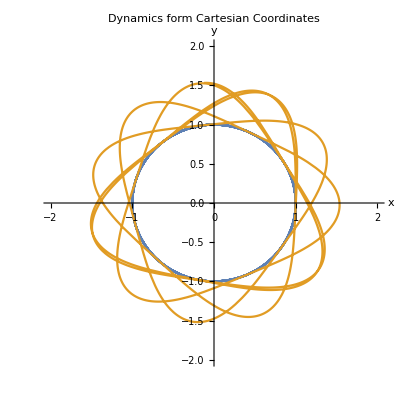

```mathematica
ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.s]},{t,0,16π},PlotRange->{{-2,2},{-2,2}},AxesLabel->{x,y},PlotLabel-> "Dynamics form Cartesian Coordinates"]
```

```mathematica
(*gifcart = Table[ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.s]},{t,0,τ},PlotRange->{{-2,2},{-2,2}},AxesLabel->{x,y},PlotLabel-> "Dynamics form Cartesian Coordinates"],{τ,0,48}];
Export["Cart_Bump.gif",gifcart];*)
```

```mathematica
Animate[ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.s10]},{t,0,τ},PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{τ,0,48}]
```

```mathematica
(*gifcart10 = Table[ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.s10]},{t,0,τ},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{x,y},PlotLabel-> "Dynamics form Cartesian Coordinates - α=10"],{τ,0,48}];
Export["Cart_Bump10.gif",gifcart10];*)
```

```mathematica
Animate[ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.s100]},{t,0,τ},PlotRange->{{-2,2},{-2,2}}],{τ,0,20}]
```

```mathematica
(*gifcart100 = Table[ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.s100]},{t,0,τ},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{x,y},PlotLabel-> "Dynamics form Cartesian Coordinates - α=100"],{τ,0,48}];
Export["Cart_Bump100.gif",gifcart100];*)
```

We observe oscillating behaviour in the well around r=R which becomes less when α gets larger.

```mathematica
sw01= NDSolve[{x''[t] == rdd[[1]],y''[t] == rdd[[2]],x[0]==1,y[0]==0,x'[0]==0,y'[0]==0.1},{x,y},{t,200}](* Taking the initial velocity a factor 10 lower*)
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
Animate[ParametricPlot[{{Cos[t],Sin[t]},Evaluate[{x[t],y[t]}/.sw01]},{t,0,τ}],{τ,0,100}]
```

The same idea of making the circle “smoother” can be used by slowing down the initial velocity

#### Working towards a 3D animation

```mathematica
Animate[
ParametricPlot3D[{{Cos[t],Sin[t],0},{Evaluate[{x[t],y[t],(√(x[t]^2+y[t]^2)-1)^2}/.s]}},{t,0,τ},
PlotRange->{{-1.5,1.5},{-1.5,1.5}},
AxesLabel->{x,y},
PlotLabel-> "Dynamics form Cartesian Coordinates"],
{τ,0,48}]
```

```mathematica
p1 = ParametricPlot3D[{{r Cos[t],r Sin[t],(r-1)^2}},{r,0.2,1.8},{t,0,2π},
PlotRange->{{-1.8,1.8},{-1.8,1.8}},
AxesLabel->{x,y,V},
PlotLabel-> "Dynamics form Cartesian Coordinates"]
```

-Graphics3D-

```mathematica
p2 =ParametricPlot3D[{{Cos[t],Sin[t],0},{Evaluate[{x[t],y[t],(√(x[t]^2+y[t]^2)-1)^2}/.s]}},{t,0,14π},
PlotRange->{{-1.8,1.8},{-1.8,1.8}},
AxesLabel->{x,y,V},
PlotLabel-> "Dynamics Derived form Cartesian and Polar Coordinates",
PlotStyle-> {{Red},{Blue}}];
Show[p1,p2]
```

-Graphics3D-